```mathematica
Clear["Global`*"]
```

```mathematica
a=50;
```

m,n are used to index one of the basis from our orthonormal basis set
Let m,n={-1,0,1} , then (n-m)_(m,n)=(0 | -1 | -2
1 | 0 | -1
2 | 1 | 0). We see that this is a Toeplitz matrix.

```mathematica
g[x_,a_,b_]:=ⅇ^(-a*(x-b)^2)
```

```mathematica
alpha=1/25;
```

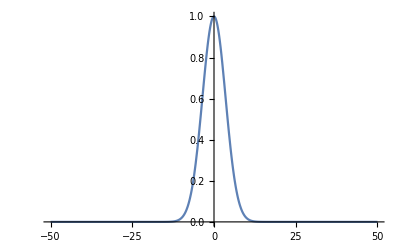

```mathematica
Plot[g[x,alpha,0],{x, -a, a},PlotRange->All]
```

We will need enough Gaussian basis to fill our numerical region of interest. So we need center our Gaussians throughout the region [-a, a].

Here, were are going to consider a small system of three Gaussian basis with manually assigned coefficients (to keep things in a form that they can be computed).

Because  the potential is a real function, the coefficients of the Gaussian basis will also be real (if the function was imaginary, they would be complex).

```mathematica
c1=7.7;
c2=-9.2;
c3=3.0;
fg[x_]:=c1*g[x,alpha,20]+c2*g[x,alpha,0]+c3*g[x,alpha,-20]
```

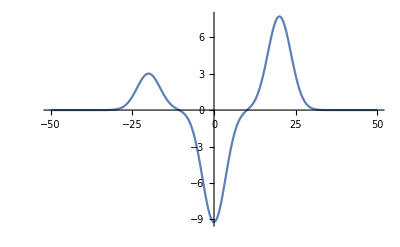

```mathematica
Plot[fg[x],{x, -a, a}, PlotRange->All]
```

```mathematica
f[x_,m_,n_]:=ⅇ^(ⅈ*π*(n-m)*x/a)*fg[x]
```

```mathematica
Vtrue=N[1/(2*a)*({{Integrate[f[x,-1,-1],{x,-a,a}], Integrate[f[x,-1,0],{x,-a,a}], Integrate[f[x,-1,1],{x,-a,a}]}, {Integrate[f[x,0,-1],{x,-a,a}], Integrate[f[x,0,0],{x,-a,a}], Integrate[f[x,0,1],{x,-a,a}]}, {Integrate[f[x,1,-1],{x,-a,a}], Integrate[f[x,1,0],{x,-a,a}], Integrate[f[x,1,1],{x,-a,a}]}})];
```

```mathematica
Vtrue//MatrixForm
```

(0.132934 | -0.50957+0.386486 ⅈ | -1.43376+0.221819 ⅈ
-0.50957-0.386486 ⅈ | 0.132934 | -0.50957+0.386486 ⅈ
-1.43376-0.221819 ⅈ | -0.50957-0.386486 ⅈ | 0.132934)

Below is a calculation of Vtrue but in vector form and then converted back to a matrix (for testing of method for converting back to matrix)

```mathematica
fs[x_,h_]:=ⅇ^(-ⅈ*π*h*x/a)*fg[x]
```

```mathematica
vctr=1/(2a)*Integrate[fs[x,{-2,-1,0,1,2}],{x,-a,a}]
```

{-1.43376+0.221819 ⅈ,-0.50957+0.386486 ⅈ,0.132934,-0.50957-0.386486 ⅈ,-1.43376-0.221819 ⅈ}

```mathematica
Vtrm=ToeplitzMatrix[vctr[[3;;]],vctr[[3;;1;;-1]]];
```

```mathematica
Vtrm//MatrixForm
```

(0.132934+0. ⅈ | -0.50957+0.386486 ⅈ | -1.43376+0.221819 ⅈ
-0.50957-0.386486 ⅈ | 0.132934+0. ⅈ | -0.50957+0.386486 ⅈ
-1.43376-0.221819 ⅈ | -0.50957-0.386486 ⅈ | 0.132934+0. ⅈ)

```mathematica
Vtrue-Vtrm//MatrixForm
```

(0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ)

We define h=-(n-m) and let m,n={-1,0,1}, then h={-2,-1,0,1,2}. We also define k_h=(π h)/a.

The Fourier transform approximation of the potential matrix is the vector Ṽ(k_h) which can be transformed into a Toeplitz matrix where the top row is negative size side of h and the left column is the positive, where the top left corner is 0 for both positive and negative.

```mathematica
k[h_]:=(π*h)/a
```

```mathematica
es[kh_]:=c1*ⅇ^(-ⅈ*kh*2)+c2+c3*ⅇ^(ⅈ*kh*2)
```

```mathematica
Vhf=1/(2*a)*√(π/alpha)ⅇ^(-k[{-2,1,0,1,2}]^2/(4*alpha))*es[{-2,1,0,1,2}]
```

{-1.30028-0.285603 ⅈ,-1.18046-0.369516 ⅈ,0.132934,-1.18046-0.369516 ⅈ,-1.30028+0.285603 ⅈ}

```mathematica
Vaprox=ToeplitzMatrix[Vhf[[3;;]],Vhf[[3;;1;;-1]]];
```

```mathematica
Vaprox//MatrixForm
```

(0.132934+0. ⅈ | -1.18046-0.369516 ⅈ | -1.30028-0.285603 ⅈ
-1.18046-0.369516 ⅈ | 0.132934+0. ⅈ | -1.18046-0.369516 ⅈ
-1.30028+0.285603 ⅈ | -1.18046-0.369516 ⅈ | 0.132934+0. ⅈ)

```mathematica
Vtrue-Vaprox//MatrixForm
```

(-5.55112×10^-17+0. ⅈ | 0.670887+0.756001 ⅈ | -0.133488+0.507421 ⅈ
0.670887-0.0169699 ⅈ | -5.55112×10^-17+0. ⅈ | 0.670887+0.756001 ⅈ
-0.133488-0.507421 ⅈ | 0.670887-0.0169699 ⅈ | -5.55112×10^-17+0. ⅈ)

```mathematica
Norm[Vtrue-Vaprox]
```

1.44834

The output of the Fourier approximation seems close but not close enough to use numerically, so I’ll check it against my calculation which uses the error function

```mathematica
s1[kh_,b_]:=√alpha*(-a-b)+(ⅈ*kh)/(2*√alpha)
s2[kh_,b_]:=√alpha*(a-b)+(ⅈ*kh)/(2*√alpha)
```

```mathematica
ers[kh_,b_]:=-Erf[s1[kh,b]]+Erf[s2[kh,b]]
```

```mathematica
erts[kh_]:=c1*ⅇ^(-ⅈ*kh*2)*ers[kh,2]+c2*ers[kh,0]+c3*ⅇ^(ⅈ*kh*2)*ers[kh,-2]
```

```mathematica
Vher=1/(4*a)*√(π/alpha)ⅇ^(-k[{-2,1,0,1,2}]^2/(4*alpha))*erts[{-2,1,0,1,2}]
```

{-1.30028-0.285603 ⅈ,-1.18046-0.369516 ⅈ,0.132934,-1.18046-0.369516 ⅈ,-1.30028+0.285603 ⅈ}

```mathematica
Ver=ToeplitzMatrix[Vher[[3;;]],Vher[[3;;1;;-1]]];
```

```mathematica
Ver//MatrixForm
```

(0.132934+0. ⅈ | -1.18046-0.369516 ⅈ | -1.30028-0.285603 ⅈ
-1.18046-0.369516 ⅈ | 0.132934+0. ⅈ | -1.18046-0.369516 ⅈ
-1.30028+0.285603 ⅈ | -1.18046-0.369516 ⅈ | 0.132934+0. ⅈ)

```mathematica
Vtrue-Ver//MatrixForm
```

(-5.55112×10^-17+0. ⅈ | 0.670887+0.756001 ⅈ | -0.133488+0.507421 ⅈ
0.670887-0.0169699 ⅈ | -5.55112×10^-17+0. ⅈ | 0.670887+0.756001 ⅈ
-0.133488-0.507421 ⅈ | 0.670887-0.0169699 ⅈ | -5.55112×10^-17+0. ⅈ)

```mathematica
Norm[Vtrue-Ver]
```

1.44834